# Chapter. Electrochemistry of thin layers and thin films

In this notebook you are asked to load data from the SERM/Data folder. To prepare for this copy the line below to an input cell, replace the file path with the file path for the "Data" folder on your computer and press ⌤
AppendTo[$Path,”(* path to *)/SERM/Data/chapter10”];
or
AppendTo[$Path,ToFileName[ {NotebookDirectory[],”Data”,”chapter10”}]];

Mathematica Preliminaries

### General

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"]];
```

```mathematica
SetSystemOptions["TypesetOptions"->{"IconicElidedForms"->False}];
```

```mathematica
CurrentValue[$FrontEnd,{SpellingDictionaries,"CorrectWords"}]=Union@Join[CurrentValue[$FrontEnd,{SpellingDictionaries,"CorrectWords"}],{"Bioanalytical","chronoamperogram","chronoamperometric","Chronoamperometric","chronoamperometry","Chronoamperometry","chronopotentiogram","chronopotentiometric","chronopotentiometry","electroactive","electroanalytical","electrochemists","eqn","eqns","Faradaic","Feldberg","Fick's","kth","Louiville","Nernst","Nicolson","overpotential","overpotentials","Richtmyer","Rieman","Semiintegration","Volmer","voltammetric","Voltammetric","voltammetry","voltammogram","voltammograms"}];
```

```mathematica
SetOptions[Plot,
Axes-> False,
BaseStyle->Directive[FontFamily-> "Arial",10,Plain],
Frame->True,
FrameLabel-> None,
FrameStyle->Directive[Black,AbsoluteThickness[.5]],
GridLines->None,
ImagePadding->{{Inherited,5},{Inherited,5}},
ImageSize->288,
PlotStyle->Directive[Black,AbsoluteThickness[.5]]];
```

```mathematica
SetOptions[ListPlot,
Axes->False,
BaseStyle->Directive[FontFamily-> "Arial",10,Plain],
Frame->True,
FrameStyle->Directive[Black,AbsoluteThickness[.5]],
GridLines->None,
ImagePadding->{{Inherited,5},{Inherited,5}},
ImageSize->288,
Joined->True,
PlotLabel->None,
PlotStyle->Directive[Black,AbsoluteThickness[.5]]];
```

```mathematica
SetOptions[ListLogPlot,
BaseStyle->Directive[FontFamily->"Arial",10,Plain],
ImagePadding->{{Inherited,5},{Inherited,5}},
ImageSize->288,
LabelStyle->Directive[FontFamily->"Arial",10,Plain],
PlotStyle->AbsolutePointSize[5],
Joined->False];
```

```mathematica
SetOptions[Plot3D,
AspectRatio-> 1,
AxesEdge->{{1,-1},{-1,-1},{1,1}},
AxesStyle->AbsoluteThickness[1],
Boxed-> True,
BoxRatios->{1,1,.7},
BoxStyle->AbsoluteDashing[{2.5,2.5}],
ImageSize->288,
Lighting-> Automatic,
Mesh->False,
PlotRange->All,
ViewVertical->{0,0,1},
ViewPoint->{2,-.5,1}];
```

```mathematica
SetOptions[ListPlot3D,
AspectRatio-> 1,
Axes->True,
AxesEdge->{{-1,-1},{1,-1},{1,1}},
AxesStyle->AbsoluteThickness[1],
Boxed-> True,
BoxRatios->{1,1,.7},
BoxStyle->AbsoluteDashing[{2.5,2.5}],
ImageSize->288,
LabelStyle->Directive[FontFamily->"Arial",10,Plain],
Lighting-> Automatic,
Mesh->False,
PlotRange->All,
ViewVertical->{0,0,1},
ViewPoint->{2,-.5,1}];
```

```mathematica
(* tick function for labelled axes or frames *)
ticks1[min_,max_,steps_,divs_]:=Join[Table[{x,Which[
Chop[x]==0,0,
0<x<2,NumberForm[x,{2,2},NumberPadding->{"","0"}],
x≥2,NumberForm[x,{2,0},NumberPadding->{"","0"}],
0>x≥-2,NumberForm[x,{2,2},NumberPadding->{"0","0"}],
-2>x,NumberForm[x,{2,0},NumberPadding->{"","0"}]
],{0.015,0}},{x,min,max,steps}],Table[{x,"",{0.0075,0}},{x,min,max,steps/divs}]];

(* tick function for non-labelled axes or frames *)
ticks2[min_,max_,steps_,divs_]:=Chop[Join[Table[{x,"",{0.015,0}},{x,min,max,steps}],Table[{x,"",{0.0075,0}},{x,min,max,steps/divs}]]];
```

```mathematica
ClearAll[LowerDiagonalMatrix,UpperDiagonalMatrix];

LowerDiagonalMatrix[f_,n_Integer?NonNegative]:=Array[If[#≥#2,f[##],0]&,{n,n}];
UpperDiagonalMatrix[f_,n_Integer?NonNegative]:=Array[If[#≤#2,f[##],0]&,{n,n}];
```

```mathematica
ClearAll[𝒻,F,R,T];
F=N@QuantityMagnitude@EntityValue[Entity["PhysicalConstant","FaradayConstant"],"Value"];(*Faradays constant*)
R=N@QuantityMagnitude@EntityValue[Entity["PhysicalConstant","MolarGasConstant"],"Value"];(*gas constant*)
T = 298.;
𝒻=F/(R*T);
```

```mathematica
Unprotect[InverseLaplaceTransform];
InverseLaplaceTransform[i_[s]/(√s), s_, t_] := 1/(√π)*∫_0^t i[τ]/(√(t-τ))ⅆτ;

(*Protect[InverseLaplaceTransform];*)
```

This for Mathematica Version 4.0 and above

```mathematica
If[$VersionNumber>3.,
Unprotect[LaplaceTransform];

LaplaceTransform[Derivative[d__][c][args__],t_,s_]:=With[{pos=Position[{args},t]},Derivative[Sequence@@Delete[{d},pos⟦1,1⟧]][C[s]][Sequence@@(Delete[{args},pos⟦1,1⟧]/.t->s)]/;Length[pos]===1&&{d}[[pos⟦1,1⟧]]===0];
LaplaceTransform[Derivative[d__][u][args__],t_,s_]:=With[{pos=Position[{args},t]},Derivative[Sequence@@Delete[{d},pos⟦1,1⟧]][U[s]][Sequence@@(Delete[{args},pos⟦1,1⟧]/.t->s)]/;Length[pos]===1&&{d}[[pos⟦1,1⟧]]===0];
LaplaceTransform[Derivative[d__][v][args__],t_,s_]:=With[{pos=Position[{args},t]},Derivative[Sequence@@Delete[{d},pos⟦1,1⟧]][V[s]][Sequence@@(Delete[{args},pos⟦1,1⟧]/.t->s)]/;Length[pos]===1&&{d}[[pos⟦1,1⟧]]===0];
LaplaceTransform[c[args__],t_,s_]:=With[{pos=Position[{args},t]},C[s][Sequence@@(Delete[{args},pos⟦1,1⟧]/.t->s)]/;Length[pos]===1]

(*Protect[LaplaceTransform];*)];
```

### Notebook specific

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
Off[NDSolve::"bdisc"];
```

```mathematica
SetOptions[EvaluationNotebook[],
PrintingStartingPageNumber->175,

PageHeaders->{
{Cell[TextData[{CounterBox["Page"]}],FontFamily->"Arial",FontSize->12],Cell[TextData[{"Electrochemistry of thin layers and thin films"}],FontFamily->"Arial",FontSize->12],None},
{None,Cell[TextData[CounterBox["Section",CounterFunction:>(Part[{"Introduction","Thin films","Thin layer cells","Solution using NDSolve","Finite difference methods","Summary","Further reading"},#]&)]],FontFamily->"Arial",FontSize->12], Cell[TextData[{CounterBox["Page"]}],FontFamily->"Arial",FontSize->12]}},

PageFooters->{{None,None,None},{None,None,None}},
PrintingOptions-> {
"PrintingMargins"->{{90,90},{60,90}},
"PaperSize"->{596,794},
"PageSize"->{596,794},
"PageHeaderMargins"->{60,60},
"PageFooterMargins"->{30,30},
"GraphicsPrintingFormat"->"DownloadPostScript",
"FirstPageFace"->Right,
"FirstPageHeader"->False,
"FirstPageFooter"->False,
"PrintRegistrationMarks"-> False}];
```

```mathematica
Needs["Notation`"];
```

```mathematica
α=0.5; (*transfer coefficient*)
```

```mathematica
ClearNotations[];
Symbolize[c^_];
Symbolize[Subscript[c, _]];
Symbolize[Subscript[c, _]^_];
```

```mathematica
option3={
PlotRange-> {{0,20},All},
RotateLabel->False,
PlotStyle-> {Black,AbsoluteThickness[.5]},
FrameLabel->{Style["σt",FontFamily-> "Times New Roman",10,Italic],Style["χ",FontFamily-> "Times New Roman",10],None,None},
FrameTicks->{ticks1[0,25,5,5],ticks1[-0.2,1.2,.2,4],ticks2[0,25,5,5],ticks2[-0.2,1.2,.2,4]}
};
```

```mathematica
optionA={PlotRange->{{-10.,10.},{-0.3,0.3}},
PlotStyle->{Black,AbsoluteThickness[0.7]},
FrameLabel->{Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",10,Black,Italic],Style["χ",FontFamily-> "Times New Roman",10, "Plain",Black],None,None}
};
```

```mathematica
optionB={
PlotRange->{{-15.,10.},{-0.3,0.3}},
RotateLabel->False,
PlotStyle->{Black,AbsoluteThickness[0.7]},
FrameLabel->{Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",10,Black,Italic],Style["χ",FontFamily-> "Times New Roman",10,"Plain",Black],None,None},
FrameTicks->{ticks1[-10,10,5,5],ticks1[-0.3,0.3,.1,5],ticks2[-10,10,5,5],ticks2[-0.3,0.3,.1,5]}};
```

```mathematica
optionC={
PlotRange:>  {{1,m},{0,1}},
FrameTicks-> {None,Automatic,None,Automatic},
FrameLabel->{Style["x",FontFamily-> "Times New Roman",10, "Bold"],Style["c/c^*",FontFamily-> "Times New Roman",10, "Plain",Italic],None,None},
RotateLabel-> False};
```

```mathematica
AxesLabel->{"k","j","  c"},
```

```mathematica
optionD={
AxesEdge->{{1,-1},{1,-1},{1,-1}},
ViewPoint->{2,1.0,1},
AxesLabel->{Style["j  ",FontFamily-> "Times New Roman",12,Italic],Style["k",FontFamily-> "Times New Roman",12,Italic],Style["c/c^*    ",FontFamily-> "Times New Roman",12,Italic]}
};
```

Mathematica Version 4.0 and above

```mathematica
If[$VersionNumber>3.,Unprotect[LaplaceTransform];
LaplaceTransform[Derivative[d__][c][args__],t_,s_]:=With[{pos=Position[{args},t]},Derivative[Sequence@@Delete[{d},pos⟦1,1⟧]][C[s]][Sequence@@(Delete[{args},pos⟦1,1⟧]/.t->s)]/;Length[pos]===1&&{d}[[pos⟦1,1⟧]]===0];];
```

```mathematica
$Line=0;
```

Chapter.Section Introduction

In earlier chapters we focussed on electrochemical reactions under conditions of semi-infinite diffusion. In this chapter we examine voltammetry under conditions of finite diffusion otherwise known as thin layer voltammetry. We’ll consider two types of thin layer cells in this chapter. The first type, that we’ll refer to as a thin layer cell, is the type of cell encountered in chapter 1 in which two flat working electrodes are separated by a thin space, L. The other type of cell is one in which the working electrode is separated from an impermeable barrier by a thin space, L. A physical example would be a glass slide placed across a flat electrode with a spacer of thickness L in between. This sort of cell is often used as an approximation for thin film electrodes by assuming that the film is impermeable during the course of the experiment. A more rigorous approach to modelling thin films would account for mass and charge transport between the film and the bulk solution.
We begin with Fick’s second law

(∂c_O(x,t))/(∂t)=D_O(∂^2 c_O(x, t))/(∂x^2)

Assuming no R initially present the initial condition is

c_O(x,t)=c_O^*
c_R(x,0)=0

Converting these equations to a dimensionless form by making the substitutions outlined in §1.4.1 gives

(∂c(x,t))/(∂t)=(∂^2 c(x,t))/(∂x^2)

c_O(x, 0)=1
c_R(x, 0)=0

Thin films have the boundary conditions:

((∂c_O(x,t))/(∂x))_(x=0)=(i(t))/(n F A D_O)

((∂c_O(x,t))/(∂x))_(x=L)=0

In dimensionless form the boundary conditions are

((∂c_O(x,t))/(∂x))_(x=0)=(i(t)L)/(n F A D_O c_O^*)

((∂c_O(x,t))/(∂x))_(x=1)=0

Thin layer cells have the boundary conditions:

((∂c_O(x,t))/(∂x))_(x=0)=-((∂c_O(x,t))/(∂x))_(x=L)=(i(t))/(n F A D_O)

In dimensionless form the boundary conditions are

((∂c_O(x,t))/(∂x))_(x=0)=-((∂c_O(x,t))/(∂x))_(x=1)=(i(t)L)/(n F A D_O c_O^*)

## Chapter.Section Thin films

```mathematica
Notation[ℒ[f___] ⟺ LaplaceTransform[f___,t,s]];
```

The Laplace transform of c(x,t) with respect to t is expressed as a function of x, C[s][x].

```mathematica
ℒ[c[x_,t_]]:=C[s][x];

thinFilm=ℒ[D[c[x,t],t]==D[c[x,t],{x,2}]]
```

-c[x,0]+s C[s][x]==C[s]''[x]

DSolve may be used to find C[s][x] and the initial boundary condition, c[x,0]→1, is inserted.

```mathematica
soln =DSolve[thinFilm /.
 c[x,0] -> 1, C[s][x], x]//Simplify
```

{{C[s][x]→1/s+ⅇ^(√s x) C[1]+ⅇ^(-√s x) C[2]}}

Taking the derivative with respect to x at x=1 we have

```mathematica
solnTLF=D[soln,x]/.x->1
```

{{C[s]'[1]→ⅇ^(√s) √s C[1]-ⅇ^(-√s) √s C[2]}}

```mathematica
solnTLF2=Solve[solnTLF⟦1,1,2⟧== 0,C[2]]
```

{{C[2]→ⅇ^(2 √s) C[1]}}

This result can be taken and used as a rule replacement. For example:

```mathematica
solnTLF2⟦1,1⟧
```

C[2]→ⅇ^(2 √s) C[1]

Therefore substituting the result for constant C[2] gives

```mathematica
solnTLF3=soln/.solnTLF2⟦1,1⟧
```

{{C[s][x]→1/s+ⅇ^(√s x) C[1]+ⅇ^(2 √s-√s x) C[1]}}

Taking the derivative with respect to x at x=0 we have

```mathematica
solnTLF4=D[solnTLF3,x]/.x-> 0
```

{{C[s]'[0]→√s C[1]-ⅇ^(2 √s) √s C[1]}}

Next we take the Laplace transform of the boundary condition:

```mathematica
(ℒ[i[t]]*L)/(nFA*𝒟*SuperStar[c])
```

(L ℒ[i[t]])/(c^* nFA 𝒟)

The Laplace transform of eqn (Chapter.EquationNumbered) can be solved for C[1].

```mathematica
solnTLF5=Solve[solnTLF4⟦1,1,2⟧== (L i[s])/(nFA 𝒟 SuperStar[c]),C[1]]//FullSimplify
```

{{C[1]→(L i[s])/(√s (c^* nFA 𝒟-c^* ⅇ^(2 √s) nFA 𝒟))}}

Substituting C[1] back into the expression for (c^-)_O(x,s) and setting x to zero gives the transformed dimensionless concentration at the electrode surface.

```mathematica
solnTLF6=solnTLF3/.{solnTLF5⟦1,1⟧,x-> 0}//FullSimplify
```

{{C[s][0]→1/s-(L Coth[√s] i[s])/(c^* nFA √s 𝒟)}}

(c^-)_O(0,s)=1/s-(i^-(s)L)/(n F A c_O^*D_O)(coth(s^(1/2)))/s^(1/2)

Equation (Chapter.EquationNumbered) can be rearranged to

```mathematica
Solve[C[s][0]==solnTLF6⟦1,1,2⟧,i[s]]
```

{{i[s]→-(c^* nFA 𝒟 Tanh[√s] (-1+s C[s][0]))/(L √s)}}

i^-(s)=-(s(c^-)_O(0,s)-1)(n F A c_O^*D_O)/L(tanh(s^(1/2)))/s^(1/2)

For a reversible reaction the dimensionless concentration of O at the electrode surface is

c_O(0,t)=ξ/(1+ξ) for t>0

with

ξ(t)=exp((n F/R T)(E_i+(L^2 υt/D_O)-E°'))

The Laplace transform of eqn (Chapter.EquationNumbered) is

(c^-)_O(0,s)=ℒ{(ξ(t))/(1+ξ(t))}

Substituting this into eqn (Chapter.EquationNumbered) we have

i^-(s)=-(s ℒ{(ξ(t))/(1+ξ(t))}-1)(n F A c_O^*D_O)/L(tanh(s^(1/2)))/s^(1/2)

To simplify eqn (Chapter.EquationNumbered) further note that the Laplace transform of the derivative of a function is:

```mathematica
LaplaceTransform[D[g[t],t],t,s]
```

-g[0]+s ℒ[g[t]]

s ℒ{g(x)}=ℒ{(dg(x))/dx}+g(0)

Therefore

s ℒ{(ξ(t))/(1+ξ(t))}-1=ℒ{d/dt((ξ(t))/(1+ξ(t)))}+(ξ(0))/(1+ξ(0))-1

Taking into account that if the initial potential is sufficiently positive (ξ(0))/(1+ξ(0))→1 then eqn (Chapter.EquationNumbered) reduces to

s ℒ{(ξ(t))/(1+ξ(t))}-1=ℒ{(n F L^2 υ)/(R T D_O)(ξ(t))/(1+ξ(t))^2}

Substituting this back into eqn(Chapter.EquationNumbered) gives

i^-(s)=-(n F A c_O^*D_O)/L(tanh(s^(1/2)))/s^(1/2)ℒ{(n F L^2 υ)/(R T D_O)(ξ(t))/(1+ξ(t))^2}

Equation (Chapter.EquationNumbered) can be written as

i^-(s)=-(n F A c_O^*D_O)/Lf^-(s)*h^-(s)

with

f^-(s)=(tanh(s^(1/2)))/s^(1/2)

and

h^-(s)=ℒ{(n F L^2 υ)/(R T D_O)(ξ(t))/(1+ξ(t))^2}

The inverse transform of the right hand side of eqn (Chapter.EquationNumbered) will result in a convolution integral. Mathematica is unable to perform in the inverse transform of tanh(s^(1/2))/s^(-1/2) but tables of Laplace transforms give the inverse transform as

ℒ^-1{(tanh(s^(1/2)))/s^(1/2)}=θ_2(0|ⅇ^(-π^2t))

where θ_2(0|ⅇ^(-π^2t)) is a function called a theta function (see functions.wolfram.com). Theta functions seem to be written in several different ways in the literature. The definition used in Mathematica and implemented in the function EllipticTheta is

θ_2(0|q)=2∑_(k=0)^∞ q^(1/4+k(k+1))

The convolution integral resulting from the inverse transform of eqn (Chapter.EquationNumbered) gives the equation for the current.

i(t)=-(n^2 F^2 A L υ c_O^*)/(R T)∫_0^t (ξ(t-τ))/(1+ξ(t-τ))^2 θ_2(0|ⅇ^(-π^2τ))ⅆτ

This equation must be solved numerically. However let’s consider two limiting cases. For very small values of t, corresponding to fast sweep rates, the theta function θ_2 can be approximated by (πt)^(-1/2). For example:

```mathematica
t=.1;

{EllipticTheta[2,0,Exp[-Pi^2*t]]//N,1/Sqrt[Pi*t]}
```

{1.78396,1.78412}

Equation (Chapter.EquationNumbered) then becomes

i(t)=-(n^2 F^2 A L υc_O^*)/(R T)1/π^(1/2)∫_0^t (ξ(τ))/(1+ξ(τ))^2 1/(t-τ)^(1/2)ⅆτ

Making the substitution z=στ where σ=n F L^2 υ/R T D_O this equation can be re-written as

(i(t))/(n F A c_O^*)((R T)/(n F υD_O))^(1/2)=-1/π∫_0^σt (ξ(z))/(1+ξ(z))^2 1/(σt-z)^(1/2)ⅆz

which is the equation for linear sweep voltammetry under conditions of semi-infinite diffusion. Therefore when fast sweep rates are applied voltammograms similar to those observed for semi-infinite diffusion will be observed.
For large values of t corresponding to slow sweep rates:

∫_0^t (ξ(t-τ))/(1+ξ(t-τ))^2 θ_2(0|ⅇ^(-π^2τ))ⅆτ≃(ξ(t))/(1+ξ(t))^2

This can be demonstrated by numerically integrating at chosen values of t.

```mathematica
ClearAll[L,υ,𝒟,ξ,t,τ];
L=.001;
υ=.0005;(*sweep rate*)
𝒟=1.*^-5;
ξ[t_]:=Exp[𝒻*(.25-(υ*t*L^2)/𝒟)]
t=100.;(*dimensionless time*)
```

```mathematica
{ξ[t]/(1+ξ[t])^2,NIntegrate[ξ[t-τ]/(1+ξ[t-τ])^2*2*∑_(n=0)^20 Exp[-Pi^2*τ*(n+1/2)^2],{τ,0,t},Compiled-> True]}
```

{0.0000718614,0.0000711215}

Equation (Chapter.EquationNumbered) then reduces to

i(t)=-n F V c_O^*σ  (ξ(t))/(1+ξ(t))^2

where V=A L is the volume of the thin film and σ=n F υ/R T. The dimensionless thin layer/thin film current, χ_tl, is therefore:

χ_tl(σ t)=(i(t))/(n F A c_O^* L σ)=-(ξ(t))/(1+ξ(t))^2

This can be equated to the semi-infinite diffusion voltammetric current

χ_tl(σ t)=(i(σ t))/(n F A c_O^* (σ D_O)^(1/2))1/L(D_O/σ)^(1/2)
=π^(1/2)χ(σ t)1/L(D_O/σ)^(1/2)

```mathematica
ClearAll[f,L,υ,𝒟,ξ,t,τ];
```

## Chapter.Section Thin layer cells

In thin layer cells the two boundaries are identical with the boundary condition at each surface given by eqn (Chapter.EquationNumbered).

```mathematica
soln
```

{{C[s][x]→1/s+ⅇ^(√s x) C[1]+ⅇ^(-√s x) C[2]}}

Taking the derivative with respect to x we have

```mathematica
solnTLC1=D[soln,x]/.x->1
```

{{C[s]'[1]→ⅇ^(√s) √s C[1]-ⅇ^(-√s) √s C[2]}}

Solving for the constant C[1] gives

```mathematica
solnTLC2=Solve[-solnTLC1⟦1,1,2⟧== (L i[s])/(nFA 𝒟 SuperStar[c]),C[1]]//Simplify
```

{{C[1]→ⅇ^(-2 √s) (C[2]-(ⅇ^(√s) L i[s])/(c^* nFA √s 𝒟))}}

Substituting this replacement rule into soln gives:

```mathematica
solnTLC3=soln/.solnTLC2⟦1,1⟧
```

{{C[s][x]→1/s+ⅇ^(-√s x) C[2]+ⅇ^(-2 √s+√s x) (C[2]-(ⅇ^(√s) L i[s])/(c^* nFA √s 𝒟))}}

Taking the derivative with respect to x at x=0 we have

```mathematica
solnTLC4=D[solnTLC3,x]/.x-> 0//Simplify
```

{{C[s]'[0]→(-1+ⅇ^(-2 √s)) √s C[2]-(ⅇ^(-√s) L i[s])/(c^* nFA 𝒟)}}

Solving for C[2] gives

```mathematica
solnTLC5=Solve[solnTLC4⟦1,1,2⟧== (L i[s])/(nFA 𝒟 SuperStar[c]),C[2]]//Simplify
```

{{C[2]→(ⅇ^(√s) L i[s])/(√s (c^* nFA 𝒟-c^* ⅇ^(√s) nFA 𝒟))}}

The Laplace transform of the equation for the concentration profile is therefore:

```mathematica
solnTLC6=solnTLC3/.solnTLC5⟦1,1⟧//FullSimplify
```

{{C[s][x]→1/s-(L Cosh[1/2 √s (1-2 x)] Csch[(√s)/2] i[s])/(c^* nFA √s 𝒟)}}

Since

```mathematica
Cosh[x]== Cosh[-x]
```

True

the equation will be identical at both x=0 and x=1.

```mathematica
solnTLC6/.x-> 0
```

{{C[s][0]→1/s-(L Coth[(√s)/2] i[s])/(c^* nFA √s 𝒟)}}

```mathematica
solnTLC6/.x-> 1
```

{{C[s][1]→1/s-(L Coth[(√s)/2] i[s])/(c^* nFA √s 𝒟)}}

This result can be rearranged to

```mathematica
Solve[C[s][1]==(solnTLC6/.x-> 1)⟦1,1,2⟧,i[s]]
```

{{i[s]→-(c^* nFA 𝒟 Tanh[(√s)/2] (-1+s C[s][1]))/(L √s)}}

i^-(s)=-(s(c^-)_O(0,s)-1)(n F A c_O^*D_O)/(L s^(1/2))tanh(s^(1/2)/2)

Following the steps in §Chapter.2 gives

i^-(s)=-(n F A c_O^*D_O)/(L s^(1/2))tanh(s^(1/2)/2)ℒ{(n F L^2 υ)/(RT D_O)(ξ(t))/(1+ξ(t))^2}

The inverse transform of the right hand side of eqn (Chapter.EquationNumbered) will result in a convolution integral. Mathematica is unable to perform in the inverse transform of tanh(s^(1/2)/2)/s^(1/2) but tables of Laplace transforms give the inverse transform as

ℒ^-1{(tanh(s^(1/2)))/s^(1/2)}=2θ_2(0|ⅇ^(-4 π^2 t))

Taking the inverse transform of eqn (Chapter.EquationNumbered) gives the equation for the current.

i(t)=-(2 n^2 F^2 ALυ c_O^*)/RT∫_0^t (ξ(t-τ))/(1+ξ(t-τ))^2 θ_2(0|ⅇ^(-4 π^2 τ))ⅆτ

This equation must be solved numerically.

## Chapter.Section Solution using NDSolve

In Mathematica versions 5.0 and higher reversible linear sweep voltammograms can be simulated using the function NDSolve although problems may arise due to the discontinuity in the boundary conditions. The problem is set up by entering the partial differential equation and the boundary conditions. Below the concentration profile during a linear sweep voltammogram is simulated using an expanding grid:

```mathematica
ClearAll[xList,tList,σ,result,c,x,t];

σ=1.;

xList=Join[{x,0.},Table[0.02*j,{j,50}]];
tList=Join[{t},Table[.2*j/σ,{j,0,100,.2}]];

result=c/.First[NDSolve[{D[c[x,t],t]==D[c[x,t],{x,2}],c[x,0]==1.,c[0,t]==If[t>0,Exp[10.-σ*t]/(1+Exp[10.-σ*t]),1.],c[1,t]==1.},c,xList,tList,MaxSteps-> 4000]]
```

InterpolatingFunction[{{0.,1.},{0.,20.}},<>]

The interpolating function can now be plotted. In the code below the plot limits are taken directly from the range of the interpolation function. Therefore if the range over x and t of the interpolating function is varied the plot range is adjusted automatically.

```mathematica
Plot3D[result[x,t],Evaluate[Flatten[{x,result⟦1,1⟧}]],Evaluate[Flatten[{t,result⟦1,2⟧}]],ViewPoint-> {-2.360, 3.580, 2.000}]
```

-Graphics3D-

Fig. Chapter.FigureCaption  NDSolve solution, using an expanding space grid, of the concentration profile for a reversible linear sweep voltammogram.

The dimensionless current is obtained by taking the derivative of the result at x=0. The plot below shows the dimensionless current.

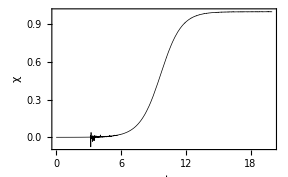

```mathematica
lsv[t_]=(D[result[x,t],x]/.x-> 0);

Plot[lsv[t/σ]/σ,{t,0.,20.},Evaluate[option3]]
```

Fig. Chapter.FigureCaption  NDSolve solution of the current for a reversible linear sweep voltammogram.

## Chapter.Section Finite difference methods

Chapter.Section.Subsection Introduction

Equation (Chapter.EquationNumbered) can be converted into a dimensionless form by making the following substitutions appropriate for voltammetry:

Δ x=L Δx

t=t/σ

σ=(n F υ)/(R T)

c_O(x,t)=c_O^*c_O(x, t)

where υ is the sweep rate.
To simulate voltammetry of thin layers and thin films we need to modify the semi-infinite simulations with the new boundary conditions. The other consideration is what value to choose for m. The previous definition of m used for the simulations of semi-infinite diffusion is unsuitable for finite diffusion. A suitable alternative might simply be to divide the thickness of the thin layer cell by Δ x. For a given sweep rate and values of n and D the size of each distance increment is defined as

Δ x=√((D Δ t)/D)

Herein lies the problem with using explicit methods to simulate thin layer voltammetry. Remembering that D<0.5 for explicit methods then for a typical diffusion coefficient of 10^-5 cm^2 · s^-1, Δ x will be approximately 4.5 · 10^-3Δ t cm. Therefore the ability to simulate voltammetry in thin layer cells with a thickness of a few microns is limited to very small time scales, i.e. very fast sweep rates. Clearly we need to be able to use large values of D which requires the use of implicit methods.
In thin layer voltammetry the dimensionless current is defined as

i(k)=(i(k))/(n F A c_O^*L σ)

To calculate the dimensionless current we begin with the equation relating the current to the concentration flux:

i(t)=-n F A (D_O((∂c_O(x,t))/(∂x)))_(x=0)

Diving both sides by n F A c_O^*L σ gives:

(i(t))/(n F A L σ c_O^*)=-D_O/(L σ)((∂c_O(x,t))/(∂x))_(x=0)

Substituting Δx=Δx/L into this equation gives the dimensionless current:

i(k)=1/(2LΔ x)(3 c_O_3^k-4 c_O_2^k+c_O_1^k)

where L is a dimensionless diffusion parameter given by

L=(L^2 σ)/D_O

To develop an expression for the dimensionless rate we begin with the Butler Volmer equation:

i(t)=n F A k_s(c_R_1(0,t)exp((1-α)(n F)/(R T)(E-E°'))-c_O_1(0,t)exp(-α(n F)/(R T)(E-E°')))

Dividing both sides by n F A L σ c_O^* gives:

(i(t))/(n F A L σ c_O^*)= k_s(c_R_1^k ξ^(1-α)-c_O_1^k ξ^-α)

with the dimensionless rate constant is defined as

k_s=k_s/(L σ)

and ξ=exp(E) with E=(n F)/(R T)(E-E°'). Combining eqns (Chapter.EquationNumbered) and (Chapter.EquationNumbered) gives

3 c_O_3^k-4 c_O_2^k+c_O_1^k= k_s(c_R_1^k ξ^(1-α)-c_O_1^k ξ^-α)

with

k_s^*=2 k_s LΔx

D=(D_O Δ t)/(Δ x)^2

Substituting Δ t=t_n/(n-1), and Δ x=L Δx gives

D=1/(Δ x)^2 D_O/L^2 t_n/(n-1)

Dividing top and bottom by σ gives

D=1/(Δ x)^2 1/L(σ t_n)/(n-1)

### Chapter.Section.Subsection Thin films

The fully implicit method requires that the system of equations shown below must be solved (see §6.5).

Yc_2^(k+1)+Zc_3^(k+1)=U
-D c_2^(k+1)+(1+2D)c_3^(k+1)-D c_4^(k+1)=c_3^k
-D c_3^(k+1)+(1+2D)c_4^(k+1)-D c_5^(k+1)=c_4^k
⋮
-D c_(j-1)^(k+1)+(1+2D)c_j^(k+1)-D c_(j+1)^(k+1)=c_j^k
⋮
-D c_(m-2)^(k+1)+(1+2D)c_(m-1)^(k+1)-D c_m^(k+1)=c_(m-1)^k

where

Y=(1+2D-(4 Dξ^α)/(3 ξ^α+2k_s^*(1+ξ)))

Z=(Dξ^α/(3 ξ^α+2k_s^*(1+ξ))-D)

and

U=c_2^k+(2 k_s^*Dξ)/(3 ξ^α+2k_s^*(1+ξ))

The boundary value at the electrode surface is

```mathematica
ClearAll[α,ξ,k,Subscript[c, O1],Subscript[c, O2],Subscript[c, O3]];

res=Solve[Subscript[c, O3]-4*Subscript[c, O2]+3*Subscript[c, O1]==k*((1-Subscript[c, O1]*ξ^(1-α))-Subscript[c, O1]*ξ^-α),Subscript[c, O1]]
```

{{c_O1→((4 c_O2-c_O3+k) ξ^α)/(k+k ξ+3 ξ^α)}}

c_O_1^k=(k_s^*ξ+ξ^α(4 c_O_2^k-c_O_3^k))/(3 ξ^α+k_s^*(ξ+1))

The difference between simulating voltammetry under semi-infinite diffusion and voltammetry under finite diffusion is the final line of eqn (Chapter.EquationNumbered). The boundary condition at the outer barrier is given by eqn (Chapter.EquationNumbered). The three point approximation for the derivative can be used to express c_m^k in terms of c_(m-1)^k and c_(m-2)^k. Since the derivative is zero at the boundary, c_m^k is

c_m^k=(4 c_(m-1)^k-c_(m-2)^k)/3

Substituting eqn (Chapter.EquationNumbered) into (Chapter.EquationNumbered) gives

Y_2 c_2^(k+1)+Z_2 c_3^(k+1)=U_2
-D c_2^(k+1)+(1+2D)c_3^(k+1)-D c_4^(k+1)=c_3^k
-D c_3^(k+1)+(1+2D)c_4^(k+1)-D c_5^(k+1)=c_4^k
⋮
-D c_(j-1)^(k+1)+(1+2D)c_j^(k+1)-D c_(j+1)^(k+1)=c_j^k
⋮
-D c_(m-3)^(k+1)+(1+2D)c_(m-2)^(k+1)-D c_(m-1)^(k+1)=c_(m-2)^k
-2/3 Dc_(m-2)^(k+1)+(1+2/3 D)c_(m-1)^(k+1)=c_(m-1)^k

Therefore the boundary condition at the outer barrier is easily included by simply altering the values of the final elements of the lower and main diagonals.

```mathematica
ClearAll[makeDiagonals];

makeDiagonals[m_Integer,𝔻_]:=Module[{x,y,z},
		x=Table[-𝔻,{m-3}];
		z=Table[-𝔻,{m-3}];
		y=Table[1.+2.*𝔻,{m-3};
AppendTo[y,1.+(2./3.)*𝔻];
AppendTo[x,-(2./3.)*𝔻]];
{x,y,z}
]
```

The maximum distance that must be considered is the thickness of the film.

x_max=(m-1)Δx=L

Substituting Δ x=(D Δ t/D)^(1/2) and Δ t=t_n/(n-1) into eqn (Chapter.EquationNumbered) gives

m=1+(L((D(n-1))/(D t_n)))^(1/2)

m=1+(L(D(n-1)))^(1/2)

A simulated reversible thin film voltammogram is shown below in Fig Chapter.FigureCaption.

```mathematica
ClearAll[c];
c=<<TFV1.dat;
```

```mathematica
ClearAll[m,𝕥,Δx,n,𝔻,𝕃,τ];
m=101;(*number of space increments*)
𝕥=40.;
Δx=0.01;
n=1027;(*1mV steps*);
𝔻=38986.4;(*model diffusion coefficient*)
𝕃=.01;
τ=𝕥/(n-1);(*calculation of the incremental time/potential step*)
```

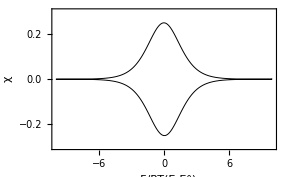

```mathematica
cv1=Map[((-#⟦3⟧+(#⟦2⟧*4)-#⟦1⟧*3)*1/(2.*𝕃*Δx))&,c];

cv2=Table[{If[j>(n+1)/2,10.-𝕥+((j-1)*τ),10.-((j-1)*τ)],cv1⟦j⟧},{j,1,Length[cv1]}];

ListPlot[cv2,PlotRange->{{-10,10},{-0.3,.3}},optionB]
```

Fig. Chapter.FigureCaption  A simulated thin film voltammogram. Simulation parameters: n=1027, D=3.9 · 10^4, L=10^-2, k_s=10^4.

The peak height and peak position are:

```mathematica
peakHeight=Min[cv2⟦All,2⟧];
Select[cv2,#⟦2⟧==peakHeight&]//Flatten;

Print["peak at ",%⟦1⟧*1000/f," mV with height ",peakHeight]
```

peak at 19.4932/f mV with height -0.249982

A quasi reversible voltammogram exhibits an asymmetrical peak shape as shown in Fig Chapter.FigureCaption.

```mathematica
ClearAll[c];

c=<<TFV2.dat;
```

```mathematica
ClearAll[𝔻,𝕃];

𝔻=38.9864;(*model diffusion coefficient*)
𝕃=10.;
```

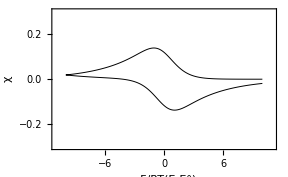

```mathematica
ClearAll[cv1,cv2];

cv1=Map[((-#⟦3⟧+(#⟦2⟧*4)-#⟦1⟧*3)*1/(2.*𝕃*Δx))&,c];

cv2=Table[{If[j>(n+1)/2,10.-𝕥+((j-1)*τ),10.-((j-1)*τ)],cv1⟦j⟧},{j,1,Length[cv1]}];

ListPlot[cv2,PlotRange->{{-11,11},{-0.3,.3}},optionB]
```

Fig. Chapter.FigureCaption  A simulated thin film voltammogram. Simulation parameters: n=1027, D=39, L=10, k_s=10^4.

The full implementation is given in the notebook implicitTFV.nb.

### Chapter.Section.Subsection Thin layer cells

In a thin layer cell an electrochemical reaction is occurring at both boundaries. At L the boundary condition can be approximated as:

(3 c_m^(k+1)-4 c_(m-1)^(k+1)+c_(m-2)^(k+1))=2 k_s^*ξ^(1-α)-2 k_s^*c_m^(k+1)ξ^(1-α)-2 k_s^*c_m^(k+1)ξ^-α

Solving for c_m^(k+1) gives: note

```mathematica
ClearAll[α,ξ,k,Subscript[c, m],Subscript[c, m-1],Subscript[c, m-2],𝔻];
res=Solve[Subscript[c, m-2]-4*Subscript[c, m-1]+3*Subscript[c, m]==2*k*ξ^(1-α)-2*k*Subscript[c, m]*ξ^(1-α)-2*k*Subscript[c, m]*ξ^-α,Subscript[c, m]]//Simplify
```

{{c_m→(2 k ξ+(4 c_(m-1)-c_(m-2)) ξ^α)/(3 ξ^α+2 k (1+ξ))}}

Substituting this result into the final line of eqn (Chapter.EquationNumbered) gives

```mathematica
(-𝔻*Subscript[c, m-2]+(1+2*𝔻)*Subscript[c, m-1]-𝔻*Subscript[c, m]==Subscript[c, m-1]^k )/.res⟦1⟧//Expand
```

c_(m-1)+2 c_(m-1) 𝔻-c_(m-2) 𝔻-(2 k 𝔻 ξ)/(3 ξ^α+2 k (1+ξ))-(4 c_(m-1) 𝔻 ξ^α)/(3 ξ^α+2 k (1+ξ))+(c_(m-2) 𝔻 ξ^α)/(3 ξ^α+2 k (1+ξ))==c_(m-1)^k

Rearranging the result gives

((D ξ^α)/(3 ξ^α+2k_s^*(1+ξ))-D)c_(m-2)^(k+1)+(1+2D-(4 Dξ^α)/(3 ξ^α+2k_s^*(1+ξ)))c_(m-1)^(k+1)=c_(m-1)^k+(2 k_s^*Dξ)/(3 ξ^α+2k_s^*(1+ξ))

Therefore for thin layer cells eqn (Chapter.EquationNumbered) can be re-written as

Yc_2^(k+1)+Zc_3^(k+1)=U_2
-D c_2^(k+1)+(1+2D)c_3^(k+1)-D c_4^(k+1)=c_3^k
-D c_3^(k+1)+(1+2D)c_4^(k+1)-D c_5^(k+1)=c_4^k
⋮
-D c_(j-1)^(k+1)+(1+2D)c_j^(k+1)-D c_(j+1)^(k+1)=c_j^k
⋮
Xc_(m-2)^(k+1)+Yc_(m-1)^(k+1)=U_(m-1)

with Y given by eqn (Chapter.EquationNumbered), X=Z where Z is given by eqn (Chapter.EquationNumbered) and U_(m-1) is

U_(m-1)=c_(m-1)^k+(2 k_s^*Dξ)/(3 ξ^α+2k_s^*(1+ξ))

Therefore the boundary conditions at both electrodes are easily included by simply altering the values of the initial and final elements of the main diagonal, the final element of the lower diagonal, and the first element of the upper diagonal at each time increment. The initial values of these elements can be set eg:

y1=yLast=1.+2.*𝔻;
z1=xLast=-𝔻;

And then the initial and final elements of the y diagonal, the final element of the x diagonal, and the first element of the z diagonal can be changed at each time step:

tmp=ξ^α/(3.*ξ^α+ ksStar*(1.+ξ));

b=Take[conc,{2,m-1}];

b⟦1⟧+=(tmp*𝔻*ksStar*ξ^(1.-α));
b⟦m-2⟧+=(tmp*𝔻*ksStar*ξ^(1.-α));

y⟦1⟧=y1-4.*𝔻*tmp;
y⟦m-2⟧=yLast-4.*𝔻*tmp;
x⟦m-2⟧=xLast+𝔻*tmp;
z⟦1⟧=z1+𝔻*tmp;

The full implementation is given in the notebook implicitTLV.nb.

```mathematica
ClearAll[c];

c=<<TLV.dat;
```

```mathematica
ClearAll[m,𝕥,Δx,n,𝔻,𝕃,τ];
m=101;(*number of space increments*)
𝕥=40.;
Δx=0.01;
n=1027;(*1mV steps*);
𝔻=38.9864;(*model diffusion coefficient*)
𝕃=10.;
τ=𝕥/(n-1);(*calculation of the incremental time/potential step*)
```

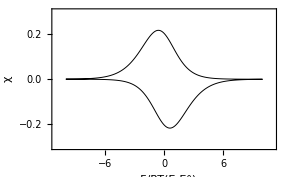

```mathematica
ClearAll[cv1,cv2];

cv1=Map[((-#⟦3⟧+(#⟦2⟧*4)-#⟦1⟧*3)*1/(𝕃*Δx))&,c];

cv2=Table[{If[j>(n+1)/2,10.-𝕥+((j-1)*τ),10.-((j-1)*τ)],cv1⟦j⟧},{j,1,Length[cv1]}];

ListPlot[cv2,PlotRange->{{-11,11},{-0.3,.3}},optionB]
```

Fig. Chapter.FigureCaption  A simulated thin layer voltammogram. Simulation parameters: n=1027, D=39, L=10, k_s=20.

Slices of the concentration profile can be plotted to see how it changes during the course of the simulation (Fig Chapter.FigureCaption).

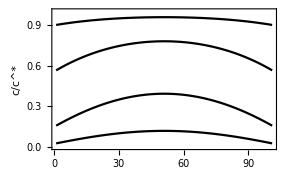

```mathematica
plot1=ListPlot[c⟦200⟧,optionC,PlotStyle-> Black];
plot2=ListPlot[c⟦250⟧,PlotStyle-> Black];
plot3=ListPlot[c⟦300⟧,PlotStyle-> Black];
plot4=ListPlot[c⟦350⟧,PlotStyle-> Black];

Show[plot1,plot2,plot3,plot4]
```

Fig. Chapter.FigureCaption  Concentration profiles during the forward sweep of the simulated thin layer voltammogram shown in Fig. Chapter.FigureCaption.

The complete concentration profile can be shown using ListPlot3D (Fig Chapter.FigureCaption).

```mathematica
ListPlot3D[c,optionD]
```

-Graphics3D-

Fig. Chapter.FigureCaption  Three dimensional plot of the concentration profile of the simulated thin layer voltammogram shown in Fig. Chapter.FigureCaption.

## Chapter.Section Summary

By limiting the diffusion space to some finite difference, L, from the electrode surface, thin layer and thin film voltammograms can be simulated in an analogous manner to semi-infinite diffusional voltammograms described in Chapter 6.

## Further reading

Aoki, K., Tokuda, K., and Matsuda, H. (1984). Journal of Electroanalytical Chemistry, 160, 33-45.
Aoki, K., Tokuda, K., and Matsuda, H. (1983). Journal of Electroanalytical Chemistry, 146, 417-24.
Hubbard, A. T. (1973). Critical Reviews in Analytical Chemistry, 3, 201-42.
Hubbard, A. T. and Anson, F. C. (1970). The Theory and Practice of Electrochemistry with Thin Layer Electrochemical Cells. In Electroanalytical Chemistry, Vol. 4. (ed. A. J. Bard), pp. 129-214. Marcel Dekker, New York.
Woodward, F. E. and Reilley, C. N. (1984). Thin Layer Cell Techniques. In Comprehensive Treatise of Electrochemistry, Vol. 9. (eds. Yeager, E., Bockris, J. O. M., Conway, B. E., and Sarangapani, S.), pp. 353-92. Plenum, New York.